# A generalized model for the charge transport properties of dressed quantum Hall systems

## Numerical Calculations

## Import packages and define global parameters

```mathematica
ClearAll["Global`*"]
<<MaTeX`
Needs["CustomTicks`"];
imageScale=72/2.54;
```

## System parameter analysis

### Constants

```mathematica
e = Quantity[(1.602176)*10^(-19),"Coulombs"];  (*electron's charge*)
hbar = Quantity[(1.054571)*10^(-34),("Kilograms"*"Meters"^2)/"Seconds"]; (*Plank's constant*)
m= Quantity[(9.109383)*10^(-31),"Kilograms"]; (*electron's mass*)
c = Quantity[(2.997924)*10^(8),"Meters"/"Seconds"]; (*speed of light in vacuum*)
ϵ0 = Quantity[(8.854187)*10^(-12),("Coulombs"^2*"Seconds"^2)/("Kilograms"*"Meters"^(3))]; (*vacuum permittivity*)
eV = Quantity[(1.602176)*10^(-19),("Kilograms"*"Meters"^2)/("Seconds"^(2))]; (*electron Volts*)
```

### System parameters

```mathematica
B = Quantity[(1.2),"Kilograms"/("Coulombs"*"Seconds")]; (*Stationary magnetic field's amplitude = 1.2 T*)
ElecInt0= Quantity[(1)*10^(6),"Kilograms"/"Seconds"^(3)]; (*Reference dressing electric field's intensity = 100 Wcm^-2*)
ω = Quantity[(2)*10^(12),"Seconds"^(-1)]; (*Dressing field's frequency = 2×10^12 rads^-1*)
me = 0.071*m;  (*Effective electron's mass for 2DEG = 0.071m*)
```

### Parameter calculation

```mathematica
ω0 = (e*B)/(me);(*cyclotron frequency*) 
E0 = Sqrt[(2*ElecInt0)/(c*ϵ0 )];(*Reference dressing electric field's amplitude*)
b= (e*E0*((ω0 )^2))/(hbar*ω*((ω0 )^2-(ω)^2));(*Pre-defined parameter*)
κ = Sqrt[me*ω0 /hbar]; (*Pre-defined parameter in Gauss-Hermite functions*)
λs1 = (hbar* b)/(e*B)(*Pre-defined parameter in inverse scattering time*)
λs2 = (hbar *κ )/(e*B) (*Pre-defined parameter in inverse scattering time*)
```

2.08959×10^-8 m

2.34203×10^-8 m

### Parameter values

```mathematica
k0 =Quantity[1*10^(8),"Meters"^(-1)];
```

```mathematica
λ1 = N[λs1*k0]
```

2.08959

```mathematica
λ2 = N[λs2*k0,4]
```

2.34203

## Landau level wavefunction χ_N

```mathematica
χ[y_?NumericQ,N_?NumericQ]:= Exp[-y^2/2]/(√(2^N*N!*√π))HermiteH[N,y];
```

We can define normalized dressed electric field intensity = ElecInt := (Real electric field intensity)/ElecInt0 where ElecInt0 =  100 Wcm^-2.

## Inverse scattering time matrix central element analysis (l=0)

### Landau level N=0

```mathematica
Q0:= χ[λ2*k2,0]*χ[λ2*(k1-k2),0];
A0[k1_?NumericQ,ElecInt_?NumericQ]:=((BesselJ[0,λ1 *Sqrt[ElecInt]*(k1)])^2)*((NIntegrate[Q0,{k2,-Infinity,Infinity},AccuracyGoal->4])^2);
Sup0 := NIntegrate[A0[k1,eInt],{k1,-Infinity,Infinity},AccuracyGoal->4];
Sdown0:= NIntegrate[A0[k1,0],{k1,-Infinity,Infinity},AccuracyGoal->4];
Tinverse0 := Sup0/Sdown0;
```

### Landau level N=1

```mathematica
Q1:= χ[λ2*k2,1]*χ[λ2*(k1-k2),1];
A1[k1_?NumericQ,ElecInt_?NumericQ]:=((BesselJ[0,λ1 *Sqrt[ElecInt]*(k1)])^2)*((NIntegrate[Q1,{k2,-Infinity,Infinity},AccuracyGoal->4])^2);
Sup1:= NIntegrate[A1[k1,eInt],{k1,-Infinity,Infinity},AccuracyGoal->4];
Sdown1:= NIntegrate[A0[k1,0],{k1,-Infinity,Infinity},AccuracyGoal->4];
Tinverse1 := Sup1/Sdown1;
```

### Landau level N=2

```mathematica
Q2:= χ[λ2*k2,2]*χ[λ2*(k1-k2),2];
A2[k1_?NumericQ,ElecInt_?NumericQ]:=((BesselJ[0,λ1 *Sqrt[ElecInt]*(k1)])^2)*((NIntegrate[Q2,{k2,-Infinity,Infinity},AccuracyGoal->4])^2);
Sup2:= NIntegrate[A2[k1,eInt],{k1,-Infinity,Infinity},AccuracyGoal->4];
Sdown2:= NIntegrate[A0[k1,0],{k1,-Infinity,Infinity},AccuracyGoal->4];
Tinverse2 := Sup2/Sdown2;
```

### Landau level N=3

```mathematica
Q3:= χ[λ2*k2,3]*χ[λ2*(k1-k2),3];
A3[k1_?NumericQ,ElecInt_?NumericQ]:=((BesselJ[0,λ1 *Sqrt[ElecInt]*(k1)])^2)*((NIntegrate[Q3,{k2,-Infinity,Infinity},AccuracyGoal->4])^2);
Sup3:= NIntegrate[A3[k1,eInt],{k1,-Infinity,Infinity},AccuracyGoal->4];
Sdown3:= NIntegrate[A0[k1,0],{k1,-Infinity,Infinity},AccuracyGoal->4];
Tinverse3:= Sup3/Sdown3;
```

### Landau level N=4

```mathematica
Q4:= χ[λ2*k2,4]*χ[λ2*(k1-k2),4];
A4[k1_?NumericQ,ElecInt_?NumericQ]:=((BesselJ[0,λ1 *Sqrt[ElecInt]*(k1)])^2)*((NIntegrate[Q4,{k2,-Infinity,Infinity},AccuracyGoal->4])^2);
Sup4:= NIntegrate[A4[k1,eInt],{k1,-Infinity,Infinity},AccuracyGoal->4];
Sdown4:= NIntegrate[A0[k1,0],{k1,-Infinity,Infinity},AccuracyGoal->4];
Tinverse4:= Sup4/Sdown4;
```

#### Generating figures

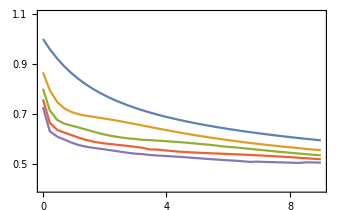

```mathematica
P1=Plot[{Sqrt[Tinverse0],Sqrt[Tinverse1],Sqrt[Tinverse2],Sqrt[Tinverse3],Sqrt[Tinverse4]} ,{eInt,0,9},
PlotRange->{{0,9},{0.4,1.1}},
PlotLegends->{MaTeX["N=1",FontSize->17],MaTeX["N=2",FontSize->17],MaTeX["N=3",FontSize->17],MaTeX["N=4",FontSize->17],MaTeX["N=5",FontSize->17]},
MaxRecursion->0,
PlotPoints->40,
Axes->False,
Frame->{{True,True},{True,True}},
FrameTicksStyle->{{FontSize->18,None},{FontSize->18,None}},
FrameTicks->{{LinTicks[{0.5,0.7,0.9,1.1},Range[0.4,1.1,0.02]],None},{LinTicks[{0,2,4,6,8},Range[0,9,0.5]],None}},
FrameLabel->{{MaTeX["\\Lambda_{N}",FontSize->17],None},{MaTeX["I(100~\\text{W}\\text{cm}^{-2})",FontSize->17],None}},
ImageSize->12*imageScale]
```

Generate normalized inverse scattering time matrix central element (Λ_N) arrays for different intensity levels:

```mathematica
Table[Sqrt[Tinverse0],{eInt,{0,1,4,9,16,25,49}}] (*N=0*)
Table[Sqrt[Tinverse1],{eInt,{0,1,4,9,16,25,49}}] (*N=1*)
Table[Sqrt[Tinverse2],{eInt,{0,1,4,9,16,25,49}}] (*N=2*)
Table[Sqrt[Tinverse3],{eInt,{0,1,4,9,16,25,49}}] (*N=3*)
Table[Sqrt[Tinverse4],{eInt,{0,1,4,9,16,25,49}}] (*N=4*)
```

{1.,0.854594,0.687531,0.593683,0.533322,0.490048,0.43024}

{0.866026,0.703668,0.6345,0.553974,0.4998,0.460621,0.406149}

{0.800388,0.650208,0.590168,0.533346,0.482439,0.445397,0.391947}

{0.757772,0.611426,0.552806,0.518009,0.47183,0.435054,0.384605}

{0.726563,0.581,0.530718,0.504442,0.461325,0.429476,0.378184}

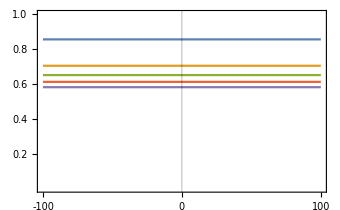

```mathematica
eInt=1;
P2=Plot[{Sqrt[Tinverse0],Sqrt[Tinverse1],Sqrt[Tinverse2],Sqrt[Tinverse3],Sqrt[Tinverse4]} ,{kx,-100,100},
PlotRange->{{-100,100},{0,1}},
PlotLegends->{MaTeX["N=1",FontSize->17],MaTeX["N=2",FontSize->17],MaTeX["N=3",FontSize->17],MaTeX["N=4",FontSize->17],MaTeX["N=5",FontSize->17]},
GridLines->{{{0,Black}},None},
MaxRecursion->0,
PlotPoints->50,
Axes->False,
Frame->{{True,True},{True,True}},
FrameTicksStyle->{{FontSize->18,None},{FontSize->18,None}},
FrameTicks->{{LinTicks[{0.2,0.4,0.6,0.8,1.0},Range[0,1.0,0.05]],None},{LinTicks[{-100,-50,0,50,100},Range[-100,100,10]],None}},
FrameLabel->{{MaTeX["\\Lambda_{N}",FontSize->17],None},{MaTeX["k_x(\\mathring{\\text{A}}^{-1})",FontSize->17],None}},
LabelStyle->{{{FontFamily->"Times New Roman"},None},{FontFamily->"Times New Roman",None}},
ImageSize->12*imageScale]
```

## Manipulate conductivity using dressing field intensity

Normalized conductivity function:

```mathematica
σ[x_,n_,Λ0_,Λ1_] =(n+1)/(0.0037*Λ0*Λ1)* (1/(1+((x-n-1)/(0.06*Λ0))^2))*(1/(1+((x-n)/(0.06*Λ1))^2));
```

Normalized inverse scattering time matrix central element (Λ_N) arrays for different intensity levels:

```mathematica
I0 = List[1.0000,0.8660,0.8004,0.7578,0.7266,0.7021,0.6821,0.6653,0.6507,0.6380,0.6267];
I1 = List[0.8546,0.7037,0.6502,0.6114,0.5810,0.5584,0.5416,0.5280,0.5160,0.5050,0.4948];
I4 = List[0.6875,0.6345,0.5902,0.5528,0.5307,0.5118,0.4958,0.4840,0.4730,0.4629,0.4547];
I9= List[0.5936,0.5539,0.5333,0.5180,0.5006,0.4812,0.4685,0.4564,0.4469,0.4377,0.4305];
I16= List[0.5333,0.4998,0.4824,0.4706,0.4617,0.4543,0.4470,0.4379,0.4274,0.4194,0.4125];
I25= List[0.4899,0.4606,0.4454,0.4350,0.4272,0.4208,0.4155,0.4109,0.4068,0.4029,0.3984];
I49= List[0.4301,0.4061,0.3937,0.3852,0.3787,0.3735,0.3691,0.3654,0.3602,0.3591,0.3564];
```

Getting sum of each Landau level contribution to the conductivity:

```mathematica
For[n=2;t0:=σ[x,0,Extract[I0,1],Extract[I0,2]],n<11,n++,
t0=t0 +σ[x,(n-1),Extract[I0,n],Extract[I0,n+1]]];
For[n=2;t1:=σ[x,0,Extract[I1,1],Extract[I1,2]],n<11,n++,
t1=t1 +σ[x,(n-1),Extract[I1,n],Extract[I1,n+1]]];
For[n=2;t4:=σ[x,0,Extract[I4,1],Extract[I4,2]],n<11,n++,
t4=t4 +σ[x,(n-1),Extract[I4,n],Extract[I4,n+1]]];
For[n=2;t9:=σ[x,0,Extract[I9,1],Extract[I9,2]],n<11,n++,
t9=t9+σ[x,(n-1),Extract[I9,n],Extract[I9,n+1]]];
For[n=2;t16:=σ[x,0,Extract[I16,1],Extract[I16,2]],n<11,n++,
t16=t16+σ[x,(n-1),Extract[I16,n],Extract[I16,n+1]]];
For[n=2;t25:=σ[x,0,Extract[I25,1],Extract[I25,2]],n<11,n++,
t25=t25+σ[x,(n-1),Extract[I25,n],Extract[I25,n+1]]];
For[n=2;t49:=σ[x,0,Extract[I49,1],Extract[I49,2]],n<11,n++,
t49=t49+σ[x,(n-1),Extract[I49,n],Extract[I49,n+1]]];
```

#### Generating figures:

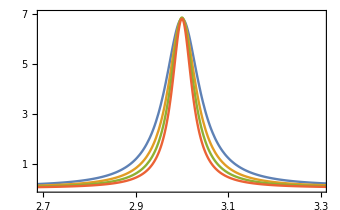

```mathematica
P3 =Plot[{t0,t1,t9,t25},{x,2.5,3.5}, 
PlotLegends->{MaTeX["I=0",FontSize->17],MaTeX["I=I_0",FontSize->17],MaTeX["I=9I_0",FontSize->17],MaTeX["I=25I_0",FontSize->17]},
PlotRange->{{2.7,3.3},{0,7}},
PlotStyle->{Thickness[0.005]},
Axes->False,
Frame->{{True,True},{True,True}},
FrameTicksStyle->{{FontSize->18,None},{FontSize->18,None}},
FrameTicks->{{LinTicks[{1,2,3,4,5,6,7},Range[0,7,0.2]],None},{LinTicks[{2.7,2.8,2.9,3.0,3.1,3.2,3.3},Range[2.7,3.3,0.02]],None}},
FrameLabel->{{MaTeX["\\widetilde{\\sigma}^{xx}",FontSize->17],None},{MaTeX["X_F",FontSize->17],None}},
LabelStyle->{{{FontFamily->"Times New Roman"},None},{FontFamily->"Times New Roman",None}},
ImageSize->12*imageScale]
```

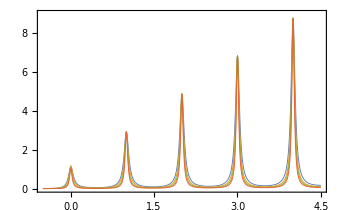

```mathematica
P4 =Plot[{t0,t1,t9,t25},{x,-0.5,4.5}, 
PlotLegends->{MaTeX["I=0",FontSize->17],MaTeX["I=I_0",FontSize->17],MaTeX["I=9I_0",FontSize->17],MaTeX["I=25I_0",FontSize->17]},
PlotRange->{{-0.5,4.5},{0,9}},
PlotStyle->{Thickness[0.002]},
Axes->False,
Frame->{{True,True},{True,True}},
FrameTicks->{{Automatic,None},{Automatic,None}},
FrameTicksStyle->{{FontSize->18,None},{FontSize->18,None}},
FrameTicks->{{LinTicks[{0,2,4,6,8},Range[0,9,0.5]],None},{LinTicks[{0,1,2,3,4},Range[-0.5,4.4,0.2]],None}},
FrameLabel->{{MaTeX["\\widetilde{\\sigma}^{xx}",FontSize->17],None},{MaTeX["X_F",FontSize->17],None}},
LabelStyle->{{{FontFamily->"Times New Roman"},None},{FontFamily->"Times New Roman",None}},
ImageSize->12*imageScale]
```

## Export figures

```mathematica
Export["fig_2.pdf",P2];
Export["fig_3.pdf",P1];
Export["fig_4.pdf",P4];
Export["fig_5.pdf",P3];
```